```mathematica
Needs["MATLink`"];
ClearAll["Global`*"];
(*OpenMATLAB[];
MEvaluate["feature('DefaultCharacterSet','windows-1252');"];
MFunction["cd"]["C:\\Users\\shyam\\SkyDrive\\Documents\\Courses\\Modeling Project\\Kinetic Model"];
modelgen= MFunction["gen_model"];
(*Specify New filenames*)	
model=modelgen["C:\\Users\\shyam\\SkyDrive\\Documents\\Courses\\Modeling Project\\TRN Model\\TRNtest8.txt"];
Vicind=IntegerPart["Vic_exind"/.model];
Vxcind=IntegerPart["Vxc_exind"/.model];
bmind=IntegerPart["bm_ind"/.model];
fluxind:=MFunction["fluxind","OutputArguments"->4];
S=Normal["S"/.model];
{vuptake,vexcrt,intind,exind}=fluxind[Vicind,Vxcind,S];
(*CloseMATLAB[];*)
DisconnectEngine[];*)

metint={M1,M2,M3};
metext={M1xt,M2xt};
protein={P1,P2,P3,P4,P5};
genes={G1,G2,G3,G4,G5};
trate={G1->P1,G2->P2,G3->P3,G4->P4,G5->P5};
fluxes={vuptake,v1,v2,v3,vexcrt,mu};
mu=0.2/3600;(*s-1*)
vin=0.00556;
alpha=40/(233/(mu*3600)^2+78);
(*gNoise=RandomReal[NormalDistribution[alpha,alpha/10],5];*)
beta=60/(82.5/(mu*3600)+148);
RNAP=3*^-5;(*uM*)
(*Gene Reactions*)
gdecay=0.0031;
pdecay=3.83*^-6;
G1prod:=Block[{brate=500,alphac=0.06,Kpm2=1*^1},
			RNAP*(alpha/brate+alphac*0*1/(1+(M2/Kpm2)^2))
		];
G2prod:=Block[{brate=500,alphac=0.06,Kp2=1*^-6},
			RNAP*((alpha/brate)+alphac*0*(P2/Kp2)/(1+(P2/Kp2)^2))
		];
G3prod:=Block[{brate=500,alphac=0.06},
			RNAP*(alpha/brate+alphac*0)
		];
G4prod:=Block[{brate=500,alphac=0.06},
			RNAP*(alpha/brate+alphac*0)
		];
gReactions:=Table[rg[i],{i,1,5}];

rg[1]:=G1prod-(gdecay+mu)*G1;
rg[2]:=G2prod-(gdecay+mu)*G2;
rg[3]:=G3prod-(gdecay+mu)*G3;
rg[4]:=G4prod-(gdecay+mu)*G4;
rg[5]:=G5prod-(gdecay+mu)*G5;
(*Protein Reactions*)
SetAttributes[translation,Listable];
translation[gp_]:=Module[{list=gp,gprod,G,P},
				G=Keys[list];
				P=Values[list];
				gprod=0.06*beta*G-(pdecay+mu)*P
				];
pReactions:=Table[translation[trate[[i]]],{i,1,5}];
(*Metabolite Reactions*)
mReactions:=Table[rm[i],{i,1,3}];
flux[sub_,prod_,spar_,ppar_,eqp_]:=Module[{S=sub,P=prod,Ks=spar,Kp=ppar,Keq=eqp,
											piP,piS,dS,dP,piSs,piPs,Vt,Vs,Vr,
											V},
	piP=Product[P[[i]],{i,1,Length[P]}];
	piS=Product[S[[i]],{i,1,Length[S]}];
	dS=1+S/Ks;
	dP=1+P/Kp;
	piSs=Product[dS[[i]],{i,1,Length[dS]}];
	piPs=Product[dP[[i]],{i,1,Length[dP]}];
	
	Vt=1-(piP/(piS*Keq));
	Vs=piS/(piSs*piPs-1);
	Vr=1;
V=Vt*Vs*Vr
];

v1:=Block[{kcat=30000,Km1=192.26,Km2=40.93,Keq=1.223},
	kcat*(P1*0.001)*flux[{M1},{M2},{Km1},{Km2},{Keq}]
		];
v2:=Block[{kcat=30000,Km1=135.98,Km3=18.25,Keq=1.223},
	kcat*(P2*0.001)*flux[{M1},{M3},{Km1},{Km3},{Keq}]
		];
v3:=Block[{kcat=30000,Km3=119.98,Km2=335.77,Keq=1.223},
	kcat*(P3*0.001)*flux[{M2},{M3},{Km2},{Km3},{Keq}]
		];
vout:=Block[{kcat=100},
	kcat*P4*0.001*M2
			];
rm[1]:=vin-v1-v2-mu*M1;
rm[2]:=v1-v3-vout-mu*M2;
rm[3]:=v2+v3-0.5*mu-mu*M3;
(*Initial Values*)
G0={G1->1.6342*^-5,G2->2.4913*^-7,G3->1.6342*^-5,G4->1.6342*^-5,G5->1.6342*^-5};
P0={P1->1.0*^-3,P2->1.5820*^-5,P3->1.0*^-3,P4->1.0*^-3,P5->1.0*^-3};
(*M0={M1->0,M2->0,M3->0};*)
M0={M1->1.2614*^3,M2->481.5724,M3->531.8574};
(*Find Roots*)
Getval[val1_,val2_]:={val1,val2};
Equations=Join[gReactions,pReactions,rm[1],rm[2],rm[3]];
varlist=Join[Keys[G0],Keys[P0],Keys[M0]];
(*val=ConstantArray[0,10];
iclist=MapThread[Getval,{Join[Keys[G0],Keys[P0]],val}];*)
iclist=MapThread[Getval,{varlist,Join[Values[G0],Values[P0],Values[M0]]}];
(*roots=FindRoot[Equations,iclist,AccuracyGoal->6,PrecisionGoal->6]*)
(*Gives only positive (feasible) solutions*)
(*sol=NSolve[Equations==0,varlist,Reals]*)
possol=Select[NSolve[Equations==0,varlist,Reals],!MemberQ[Values[#],x_/;x<0]&]
(*ListLinePlot[M1/.possol,Frame->True,FrameLabel->{"Root #","Metabolite M1 mmoles/gDCW"},
						LabelStyle->Directive[RGBColor[0.5,0.5,0.5],FontFamily->"Helevetica",FontSize->12,FontWeight->Bold],
						FrameTicks->{{1,2,3,4,5},Automatic},
						PlotMarkers->Automatic
			]
ListLinePlot[M2/.possol,Frame->True,FrameLabel->{"Root #","Metabolite M2 mmoles/gDCW"},
						LabelStyle->Directive[RGBColor[0.5,0.5,0.5],FontFamily->"Helevetica",FontSize->12,FontWeight->Bold],
						FrameTicks->{{1,2,3,4,5},Automatic},
						PlotMarkers->Automatic
			]
ListLinePlot[M3/.possol,Frame->True,FrameLabel->{"Root #","Metabolite M3 mmoles/gDCW"},
						LabelStyle->Directive[RGBColor[0.5,0.5,0.5],FontFamily->"Helevetica",FontSize->12,FontWeight->Bold],
						FrameTicks->{{1,2,3,4,5},Automatic},
						PlotMarkers->Automatic
			]
ListLinePlot[P2/.possol,Frame->True,FrameLabel->{"Root #","Protein P2 umoles/gDCW"},
						LabelStyle->Directive[RGBColor[0.5,0.5,0.5],FontFamily->"Helevetica",FontSize->12,FontWeight->Bold],
						FrameTicks->{{1,2,3,4,5},Automatic},
						PlotMarkers->Automatic
			]*)
(*negsol=NSolve[Equations==0,varlist,Reals];
negsol[[15;;-1]]*)

(*Print[M1/.solution];
Print[M2/.solution];*)
(*sol=MapThread[{#1,#2,#3,#4,#5}&,{M1/.solution,M2/.solution,M3/.solution,P2/.solution,G2/.solution}];*)
(*sol=Select[solution,!MemberQ[#,x_/;x<0]&];*)

(*f=Keys[#]:>Values[#]/;!MemberQ[Values[#],x_/;x<0]&;*)


(*Print[sol[[2]]];
For[i=1,i≤14,i++,
Print[MemberQ[sol[[i]],x_/;x<0]];
  ];*)

(*sol=MapThread[{#1,#2,#3,#4,#5}&,{G2/.solution,P2/.solution,M1/.solution,M2/.solution,M3/.solution}]*)
(*solsel={Print[sol[[2]]];
Print[sol[[4]]];
Print[sol[[5]]];
Print[sol[[12]]];};*)

(*Needs["MATLink`"];
OpenMATLAB[];
MEvaluate["feature('DefaultCharacterSet','windows-1252');"];
MFunction["cd"]["C:\\Users\\shyam\\SkyDrive\\Documents\\Courses\\Modeling Project\\TRN Model"];
Ckinetics=MFunction["ConveninceKinetics"];
*)
```

Part::partd: Part specification gNoise ⟦ 1 ⟧ is longer than depth of object.

Part::partd: Part specification gNoise ⟦ 2 ⟧ is longer than depth of object.

Part::partd: Part specification gNoise ⟦ 3 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

```mathematica
S = {    {1,-1,0,0,0,0,0,0,0,-1,0,0,0,0,0},
	{0,1,0,0,0,0,0,0,0,0,0,0,-1,0,0},
	{0,0,1,-1,0,0,0,0,0,0,-1,0,0,0,0},
	{0,0,0,1,0,0,0,0,0,0,0,0,0,-1,0},
	{0,0,0,0,1,-1,0,0,0,0,0,-1,0,0,0},
	{0,0,0,0,0,1,0,0,0,0,0,0,0,0,-1},
	{0,0,0,0,0,0,-1,-1,0,0,0,0,0,0,0},
	{0,0,0,0,0,0,1,0,-1,0,0,0,0,0,0},
	{0,0,0,0,0,0,0,1,1,0,0,0,0,0,0}};
Z={{0,z12,0,0,0,0,0,0,0},
{z21,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0},
{0,0,z43,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0},
{0,0,0,0,z65,0,0,0,0},
{0,z72,0,0,0,0,z77,0,0},
{0,0,0,z84,0,0,z87,0,0},
{0,0,0,0,0,z96,0,z98,0},
{z101,0,0,0,0,0,0,0,0},
{0,z112,0,0,0,0,0,0,0},
{0,0,z123,0,0,0,0,0,0},
{0,0,0,z134,0,0,0,0,0},
{0,0,0,0,z145,0,0,0,0},
{0,0,0,0,0,z156,0,0,0}};
(*Find basis using MATLAB and get jb and corresponding basis vectors*)
r=RowReduce[S];
Print[MatrixForm[r]];
Lstar=Transpose[NullSpace[Transpose[r]]];
L = Transpose[NullSpace[Transpose[S]]];
Print[MatrixForm[Lstar]];
Print[MatrixForm[L]];


(*r.{v1,v2,v3,v4,v5,v6,v7,v8,v9,v10,v11,v12,v13,v14,v15};
r.{v1,v2,v3,v4,v5,v6,v7,v8,0,0,0,0,0,0,1}*)
(*eqn=Thread[r.{v1,v2,v3,v4,v5,1,0,0,0}=={0,0,0,0,0,0,0,0,0,0,0,0}]*)
(*Z={{0,0,0,0,0,0,0,0,0,0,0,0},
	{0,z22,0,0,0,0,0,0,0,0,0,0},
	{0,0,0,0,0,0,0,0,0,0,0,0},
	{0,0,0,0,z45,0,0,0,0,0,0,0},
	{0,0,0,0,0,0,0,0,0,0,0,0},
	{0,0,0,0,0,0,0,z68,0,0,0,0},
	{0,0,z73,0,0,0,0,0,0,z710,0,0},
	{0,0,0,0,0,z86,0,0,0,z810,0,0},
	{0,0,0,0,0,0,0,0,z99,0,z911,0}};*)
Mstar=M=S.Z;
Print[MatrixForm[M]];
Mstar[[9]]=Flatten[L];(*Transpose[L];
Mstar[[3]]={0,0,0,0,0,0,-1,1,0,0,0,0};
Mstar[[6]]={0,0,0,0,0,0,0,1,0,0,0,0};
Mstar[[9]]={0,0,0,0,0,0,1,0,0,0,0,0};
Mstar[[12]]={0,0,0,0,0,1,0,0,0,0,0,0};*)
Print[MatrixForm[Mstar]];
Det[Mstar]
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

(0
0
0
0
0
0
0
0
1)

(0
0
0
0
0
0
1
1
1)

(-z101-z21 | z12 | 0 | 0 | 0 | 0 | 0 | 0 | 0
z21 | 0 | 0 | -z134 | 0 | 0 | 0 | 0 | 0
0 | -z112 | -z43 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | z43 | 0 | -z145 | 0 | 0 | 0 | 0
0 | 0 | -z123 | 0 | -z65 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | z65 | -z156 | 0 | 0 | 0
0 | -z72 | 0 | -z84 | 0 | 0 | -z77-z87 | 0 | 0
0 | z72 | 0 | 0 | 0 | -z96 | z77 | -z98 | 0
0 | 0 | 0 | z84 | 0 | z96 | z87 | z98 | 0)

(-z101-z21 | z12 | 0 | 0 | 0 | 0 | 0 | 0 | 0
z21 | 0 | 0 | -z134 | 0 | 0 | 0 | 0 | 0
0 | -z112 | -z43 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | z43 | 0 | -z145 | 0 | 0 | 0 | 0
0 | 0 | -z123 | 0 | -z65 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | z65 | -z156 | 0 | 0 | 0
0 | -z72 | 0 | -z84 | 0 | 0 | -z77-z87 | 0 | 0
0 | z72 | 0 | 0 | 0 | -z96 | z77 | -z98 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1)

-(-z101 z112 z123 z134 z145 z156-z112 z123 z134 z145 z156 z21-z101 z112 z134 z156 z43 z65-z112 z134 z156 z21 z43 z65) (-z77-z87) z98

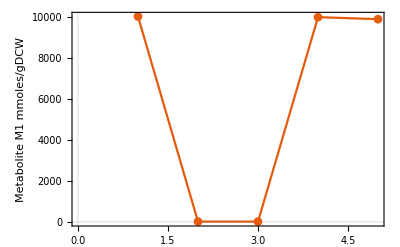

```mathematica
ListLinePlot[M1/.possol,PlotTheme->"Scientific",AxesLabel->"Metabolite M1 mmoles/gDCW",Ticks->Automatic,PlotMarkers->Automatic,LabelStyle->{12,RGBColor[0.2,0.2,0.2],Bold}]
```

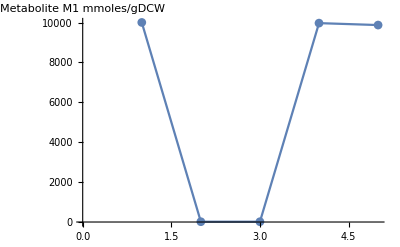

```mathematica
Show[%5512,AxesStyle->Gray]
```

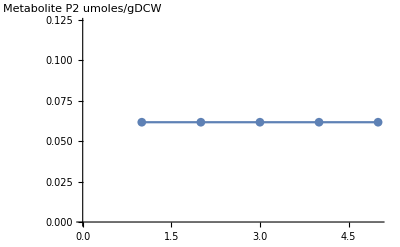

```mathematica
Show[%5455,AxesStyle->Black]
```

```mathematica
Show[%5456,PlotLabel->None,LabelStyle->{12,RGBColor[0.,0.,0.],Bold}]
```

-Graphics-

{1.28844×10^-7,1.28844×10^-7,1.28844×10^-7,1.28844×10^-7,1.28844×10^-7,1.28844×10^-7,1.28844×10^-7,1.28844×10^-7,1.28844×10^-7,1.28844×10^-7,1.28844×10^-7,1.28844×10^-7,1.28844×10^-7,1.28844×10^-7,1.28844×10^-7,1.28844×10^-7,1.28844×10^-7,1.28844×10^-7,1.28844×10^-7,1.28844×10^-7,1.28844×10^-7,1.28844×10^-7,1.28844×10^-7,1.28844×10^-7,1.28844×10^-7,1.28844×10^-7,1.28844×10^-7,1.28844×10^-7}

{0.0000139351,0.0000139351,0.0000139351,0.0000139351,0.0000139351,0.0000139351,0.0000139351,0.0000139351,0.0000139351,0.0000139351,0.0000139351,0.0000139351,0.0000139351,0.0000139351,0.0000139351,0.0000139351,0.0000139351,0.0000139351,0.0000139351,0.0000139351,0.0000139351,0.0000139351,0.0000139351,0.0000139351,0.0000139351,0.0000139351,0.0000139351,0.0000139351}

```mathematica
brate=5000;alphac=0.06;
Eqn:=alpha/brate+alphac*1/(1+((0.06*beta/((1*^-4)*(pdecay+mu)))*G)^2)==(gdecay+mu)*G/RNAP;
Eqn1:=alpha/brate==(gdecay+mu)*G/RNAP;
Eqn2:=P==(0.06*beta/((1*^-4)*(pdecay+mu)))*G;
sol=NSolve[{Eqn,Eqn2},{G,P},Reals]
```

{{G→0.0000110249,P→6.99165}}

```mathematica
{G1->1.6341762233979424*^-6,G2->1.6341762233979425*^-7,G3->1.6341762233979426*^-6,G4->1.6341762233979424*^-6,G5->1.6341762233979424*^-6,P1->0.0017272349104691619,P2->0.00017272349104691616,P3->0.001727234910469162,P4->0.0017272349104691619,P5->0.0017272349104691619,M1->2443.056747057136,M2->32.88216408975907,M3->0.0032390666819147496}
```

{G1→1.63418×10^-6,G2→-8.56103×10^-13,G3→1.63418×10^-6,G4→1.63418×10^-6,G5→1.63418×10^-6,P1→0.00172723,P2→-9.04854×10^-10,P3→0.00172723,P4→0.00172723,P5→0.00172723,M1→2443.06,M2→32.8812,M3→0.00324384}

```mathematica
Needs["MATLink`"];
ClearAll["Global`*"];
(*OpenMATLAB[];*)
MEvaluate["feature('DefaultCharacterSet','windows-1252');"];
MFunction["cd"]["C:\\Users\\shyam\\SkyDrive\\Documents\\Courses\\Modeling Project\\Kinetic Model"];
modelgen= MFunction["gen_model"];	
model=modelgen["C:\\Users\\shyam\\SkyDrive\\Documents\\Courses\\Modeling Project\\TRN Model\\TRNtest8.txt"];
Vicind=IntegerPart["Vic_exind"/.model];
Vxcind=IntegerPart["Vxc_exind"/.model];
bmind=IntegerPart["bm_ind"/.model];
fluxind:=MFunction["fluxind","OutputArguments"->4];
S=Normal["S"/.model];
{vuptake,vexcrt,intind,exind}=fluxind[Vicind,Vxcind,S];
(*CloseMATLAB[];
DisconnectEngine[];*)

metint={M1,M2,M3};
metext={M1xt,M2xt};
protein={P1,P2,P3,P4,P5};
genes={G1,G2,G3,G4,G5};
trate={G1->P1,G2->P2,G3->P3,G4->P4,G5->P5};
fluxes={vuptake,v1,v2,v3,vexcrt,mu};
mu=0.8/3600;(*s-1*)
alpha=40/(233/(mu*3600)^2+78);
beta=60/(82.5/(mu*3600)+148);
RNAP=3*^-5;(*uM*)
(*Gene Reactions*)
gdecay=0.0031;
pdecay=3.83*^-6;
G1prod:=Block[{brate=500,alphac=0.06},
			RNAP*(alpha/brate)
		];
G2prod:=Block[{brate=500,alphac=0.06,Kp2=1*^-4},
			RNAP*((alpha/brate)+alphac*((P2[t]*1*^-3/Kp2)/(1+(P2[t]*1*^-3/Kp2)))*0)
		];
G3prod:=Block[{brate=500,alphac=0.06},
			RNAP*(alpha/brate)+alphac*0
		];
G4prod:=Block[{brate=500,alphac=0.06},
			RNAP*(alpha/brate)
		];
G5prod:=Block[{brate=500,alphac=0.06},
			RNAP*(alpha/brate)
		];
gReactions:=Table[rg[i],{i,1,5}];

rg[1]:=G1prod-(gdecay+mu)*G1[t];
rg[2]:=G2prod-(gdecay+mu)*G2[t];
rg[3]:=G3prod-(gdecay+mu)*G3[t];
rg[4]:=G4prod-(gdecay+mu)*G4[t];
rg[5]:=G5prod-(gdecay+mu)*G5[t];
(*Protein Reactions*)
SetAttributes[translation,Listable];
translation[gp_]:=Module[{list=gp,gprod,G,P},
				G=Keys[list];
				P=Values[list];
				gprod=beta*G[t]-(pdecay+mu)*P[t]
				];
pReactions:=Table[translation[trate[[i]]],{i,1,5}];
(*Metabolite Reactions*)
mReactions:=Table[rm[i],{i,1,3}];
flux[sub_,prod_,spar_,ppar_,eqp_]:=Module[{S=sub,P=prod,Ks=spar,Kp=ppar,Keq=eqp,
											piP,piS,dS,dP,piSs,piPs,Vt,Vs,Vr,
											V},
	piP=Product[P[[i]],{i,1,Length[P]}];
	piS=Product[P[[i]],{i,1,Length[S]}];
	dS=1+S/Ks;
	dP=1+P/Kp;
	piSs=Product[dS[[i]],{i,1,Length[dS]}];
	piPs=Product[dP[[i]],{i,1,Length[dP]}];
	
	Vt=1-piP/(piS*Keq);
	Vs=piS/(piSs*piPs-1);
	Vr=1;
V=Vt*Vs*Vr
];

v1:=Block[{kcat=30000,Km1=192.26,Km2=40.93,Keq=1.223},
	kcat*(P1[t]*1*^-3)*flux[{M1[t]},{M2[t]},{Km1},{Km2},{Keq}]
		];
v2:=Block[{kcat=30000,Km1=135.98,Km3=18.25,Keq=1.223},
	kcat*(P2[t]*1*^-3)*flux[{M1[t]},{M3[t]},{Km1},{Km3},{Keq}]
		];
v3:=Block[{kcat=30000,Km3=119.98,Km2=335.77,Keq=1.223},
	kcat*(P3[t]*1*^-3)*flux[{M2[t]},{M3[t]},{Km2},{Km3},{Keq}]
		];
vuptake:=0.556;
vexcrt:=Block[{kcat=100},
	kcat*P5[t]*1.*^-3*M2[t]
			];
rm[1]:=vuptake-v1-v2-mu*M1[t];
rm[2]:=v1-v3-vexcrt-mu*M2[t];
rm[3]:=v2+v3-0.5*mu-mu*M3[t];
(*Initial Values*)
G0={G1->1.6342*^-5,G2->2.4913*^-7,G3->1.6342*^-5,G4->1.6342*^-5,G5->1.6342*^-5};
P0={P1->1.0*^-3,P2->1.5820*^-5,P3->1.0*^-3,P4->1.0*^-3,P5->1.0*^-3};
(*M0={M1->0,M2->0,M3->0};*)
M0={M1->1.2614*^3,M2->481.5724,M3->531.8574};
(*Find Roots*)
Getval[val1_,val2_]:={val1,val2};
Equations=Join[gReactions,pReactions,mReactions];
val=ConstantArray[0,10];
(*iclist=MapThread[Getval,{Join[Keys[G0],Keys[P0]],val}];*)
(*iclist=MapThread[Getval,{Join[Keys[G0],Keys[P0],Keys[M0]],
					Join[Values[G0],Values[P0],Values[M0]]}];*)
varlist=Join[Keys[G0],Keys[P0],Keys[M0]];
iclist=Join[Values[G0],Values[P0],Values[M0]];
(*roots=FindRoot[Equations,iclist,AccuracyGoal->4,PrecisionGoal->4];
solution=NSolve[Equations==0,Join[Keys[G0],Keys[P0],Keys[M0]],Reals];*)
(*Dsolve[]=Module[{rxn,icc,var,Eqns,t},*)
					rxn=Equations;
					icc=iclist;
					var=varlist;
					Eqns={{G1'[t]==rxn[[1]],G1[0]==icc[[1]]},{G2'[t]==rxn[[2]],G2[0]==icc[[2]]},{G3'[t]==rxn[[3]],G3[0]==icc[[3]]},  
					    {G4'[t]==rxn[[4]],G4[0]==icc[[4]]},{G5'[t]==rxn[[5]],G5[0]==icc[[5]]},
						{P1'[t]==rxn[[6]],P1[0]==icc[[6]]},{P2'[t]==rxn[[7]],P2[0]==icc[[7]]},{P3'[t]==rxn[[8]],P3[0]==icc[[8]]},
						{P4'[t]==rxn[[9]],P4[0]==icc[[9]]},{P5'[t]==rxn[[10]],P5[0]==icc[[10]]},
						{M1'[t]==rxn[[11]][[1]],M1[0]==icc[[11]]},{M2'[t]==rxn[[12]][[1]],M2[0]==icc[[12]]},
						{M3'[t]==rxn[[13]][[1]],M3[0]==icc[[13]]}
						};
			dsolution=NDSolve[Eqns,varlist,{t,0,730},Method->Automatic,PrecisionGoal->6,AccuracyGoal->6]
			(*];*)
(*Table[Plot[Evaluate[varlist[[i]][t]/.dsolution],{t,0,6000},PlotRange->All],{i,1,13}]*)
(*Plot[P2[t]/.dsolution,{t,0,6000}]*)
```

{{G1→InterpolatingFunction[{{0., 730.}}, <>],G2→InterpolatingFunction[{{0., 730.}}, <>],G3→InterpolatingFunction[{{0., 730.}}, <>],G4→InterpolatingFunction[{{0., 730.}}, <>],G5→InterpolatingFunction[{{0., 730.}}, <>],P1→InterpolatingFunction[{{0., 730.}}, <>],P2→InterpolatingFunction[{{0., 730.}}, <>],P3→InterpolatingFunction[{{0., 730.}}, <>],P4→InterpolatingFunction[{{0., 730.}}, <>],P5→InterpolatingFunction[{{0., 730.}}, <>],M1→InterpolatingFunction[{{0., 730.}}, <>],M2→InterpolatingFunction[{{0., 730.}}, <>],M3→InterpolatingFunction[{{0., 730.}}, <>]}}

```mathematica
FindRoot[
```

{4.,5.,2.,4.}

{-G1 gdecay+(alpha RNAP)/500,-G2 gdecay+(alpha RNAP)/500,-G3 gdecay+(alpha RNAP)/500,-G4 gdecay+(alpha RNAP)/500,-G5 gdecay+(alpha RNAP)/500}

{{0.556-M1 mu-(100 (1-1/Keq1) M2 P1)/(-1+(1+M1/KM11) (1+M2/KM21))-(100 (1-1/Keq2) M3 P2)/(-1+(1+M1/KM12) (1+M3/KM32))},{-M2 mu+(100 (1-1/Keq1) M2 P1)/(-1+(1+M1/KM11) (1+M2/KM21))+(100 (1-1/Keq3) M2 P3)/(-1+(1+M2/KM23) (1+M3/KM33))-0.1 M2 P5},{-M3 mu+(100 (1-1/Keq2) M3 P2)/(-1+(1+M1/KM12) (1+M3/KM32))-(100 (1-1/Keq3) M2 P3)/(-1+(1+M2/KM23) (1+M3/KM33))}}

{beta G1-P1 (mu+pdecay),beta G2-P2 (mu+pdecay),beta G3-P3 (mu+pdecay),beta G4-P4 (mu+pdecay),beta G5-P5 (mu+pdecay)}

```mathematica
{M1,M2,M3}
Keys[{G1->P1,G2->P2}]
mReactions[[1]]
```

{M1,M2,M3}

{G1,G2}

{0.556-M1 mu-(100 (1-1/Keq1) M2 P1)/(-1+(1+M1/KM11) (1+M2/KM21))-(100 (1-1/Keq2) M3 P2)/(-1+(1+M1/KM12) (1+M3/KM32))}